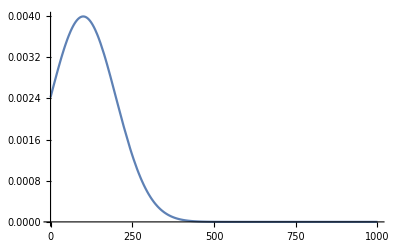

```mathematica
Plot[PDF[NormalDistribution[100,100],x],{x,0,1000},PlotRange->All]
```

```mathematica
n=10000;
τ=5;
σ0=Table[{i,If[i>τ,1,0]},{i,1,10,.1}];
dat=Join[{σ0},Table[{μ,Count[RandomVariate[NormalDistribution[μ,σ],n],x_/;x>τ]/n},{σ,{.1,1,2,10}},{μ,1,10,.1}]];
```

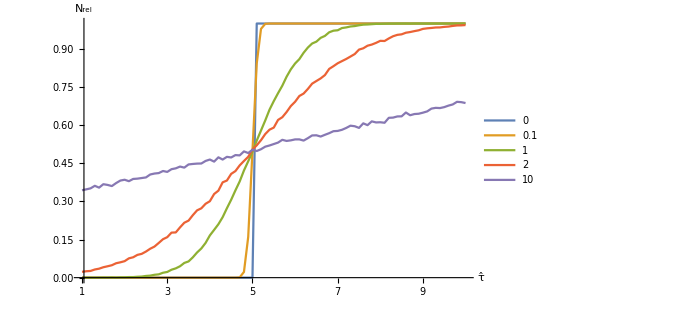

```mathematica
ListPlot[dat,Joined->True,PlotStyle-> Thick,PlotLegends->{0,.1,1,2,10},PlotRange->{{1,10},Automatic},Ticks->{Range[10],Automatic},AxesLabel->{"τ̂","N_rel" },AxesStyle->Directive[Black,24],ImageSize->{500, Automatic}]
```

```mathematica
?TicksStyle
```

TicksStyle is an option for graphics functions which specifies how ticks should be rendered.

```mathematica
PDF[NormalDistribution[0,0]]
```

NormalDistribution::posprm: Parameter 0 at position 2 in NormalDistribution[0, 0] is expected to be positive.

PDF[NormalDistribution[0,0]]

```mathematica
RandomVariate[NormalDistribution[0,0.1],10]
```

```mathematica
Count[Range[6],x_/;x≤ 3]
```

3